# Axions and the Strong CP Problem

```mathematica
$PrePrint=TraditionalForm;
```

## Pions without axions

```mathematica
Vpion = -2*a0*fπ^3 *(Mu*Cos[ϕ+θ/2]+Md*Cos[ϕ-θ/2])
```

-2 a0 fπ^3 (Md cos(θ/2-ϕ)+Mu cos(θ/2+ϕ))

```mathematica
dVpiondphi = D[Vpion,ϕ]//Simplify;
phiminsols = Solve[dVpiondphi == 0, ϕ]//Simplify;
phimin = FullSimplify[ϕ/.phiminsols[[4]],Assumptions->{Element[Mu|Md|θ,Reals],Mu>0,Md>0}];
tanphimin = FullSimplify[Tan[ϕ]/.phiminsols[[2]],Assumptions->{Element[Mu|Md|θ,Reals],Mu>0,Md>0}];
```

Solve::nsmet: This system cannot be solved with the methods available to Solve. Try Reduce or FindInstance instead.

Part::partw: Part 4 of Solve[a0 fπ (Md Sin[θ/2-ϕ]-Mu Sin[θ/2+ϕ])==0,ϕ] does not exist.

ReplaceAll::reps: {Solve[a0 fπ (Md Sin[θ/2-ϕ]-Mu Sin[θ/2+ϕ])==0,ϕ]⟦4⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ϕ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Vmin = Simplify[Vpion/.{ϕ->phimin},Assumptions->{Element[Mu|Md|θ,Reals],Mu>0,Md>0,Md>Mu,θ>0,θ<2*Pi}]
```

-2 a0 fπ^3 (Md cos(1/2 (θ-2 (ϕ/.Solve[a0 fπ (Md sin(θ/2-ϕ)-Mu sin(θ/2+ϕ))==0,ϕ]⟦4⟧)))+Mu cos((ϕ/.Solve[a0 fπ (Md sin(θ/2-ϕ)-Mu sin(θ/2+ϕ))==0,ϕ]⟦4⟧)+θ/2))

```mathematica
Vmin//TrigExpand
```

-(2 a0 fπ^3 Md^2 cos^2(θ/2))/(√(Md^2+2 Md Mu cos(θ)+Mu^2))-(2 a0 fπ^3 Mu^2 cos^2(θ/2))/(√(Md^2+2 Md Mu cos(θ)+Mu^2))-(4 a0 fπ^3 Md Mu cos^2(θ/2))/(√(Md^2+2 Md Mu cos(θ)+Mu^2))-2 a0 fπ^3 Md sin(θ/2) √(1-(cos^2(θ/2) (Md+Mu)^2)/(Md^2+2 Md Mu cos(θ)+Mu^2))+2 a0 fπ^3 Mu sin(θ/2) √(1-(cos^2(θ/2) (Md+Mu)^2)/(Md^2+2 Md Mu cos(θ)+Mu^2))

```mathematica
Simplify[%]
```

2 a0 fπ^3 (-(cos^2(θ/2) (Md+Mu)^2)/(√(Md^2+2 Md Mu cos(θ)+Mu^2))-sin(θ/2) (Md-Mu) √((sin^2(θ/2) (Md-Mu)^2)/(Md^2+2 Md Mu cos(θ)+Mu^2)))

```mathematica
Simplify[%,Assumptions->{Element[Mu|Md|θ,Reals],Mu>0,Md>0,Md>Mu,θ>0,θ<2*Pi}]
```

-2 a0 fπ^3 √(Md^2+2 Md Mu cos(θ)+Mu^2)

```mathematica
phimin
```

cos^-1((cos(θ/2) (Md+Mu))/(√(Md^2+2 Md Mu cos(θ)+Mu^2)))

```mathematica
tanphimin
```

-(sec(θ/2) Abs[sin(θ/2)] Abs[Md-Mu])/(Md+Mu)

```mathematica
tanphimin = ((Mu - Md)/(Mu+Md)) * Tan[θ/2]
```

(tan(θ/2) (Mu-Md))/(Md+Mu)

This gives the VEV of the pion. Now assume the pion oscillates about this minimum so that π  = ⟨π⟩ + π0.

```mathematica
πvev =phimin*Sqrt[2]*fπ//Simplify;
πtot = πvev + π0;
VpionNearMin = Vpion/.{ϕ -> πtot / (Sqrt[2]*fπ)}//Simplify;
```

```mathematica
VpionNearMin
```

-2 a0 fπ^3 (Md cos(1/2 (-(√2 π0)/fπ+θ-2 cos^-1((cos(θ/2) (Md+Mu))/(√(Md^2+2 Md Mu cos(θ)+Mu^2)))))+Mu cos(1/2 ((√2 π0)/fπ+θ)+cos^-1((cos(θ/2) (Md+Mu))/(√(Md^2+2 Md Mu cos(θ)+Mu^2)))))

```mathematica
pionmassterm = 2*Coefficient[Normal[Series[VpionNearMin,{π0,0,2}]],π0^2]//Simplify;
pionmassterm=Simplify[pionmassterm,Assumptions->{Element[Mu|Md|θ,Reals],Mu>0,Md>0,Md>Mu,θ>0,θ<Pi}];
pionmassterm=Simplify[TrigExpand[%],Assumptions->{Element[Mu|Md|θ,Reals],Mu>0,Md>0,Md>Mu,θ>0,θ<Pi}]
```

a0 fπ √(Md^2+2 Md Mu cos(θ)+Mu^2)

```mathematica
FullSimplify[pionmassterm]
```

a0 fπ √(Md^2+2 Md Mu cos(θ)+Mu^2)

```mathematica
pionmassterm = FullSimplify[pionmassterm];
```

```mathematica
VpionatMin=Simplify[TrigExpand[VpionNearMin/.{π0->0}]]
```

2 a0 fπ^3 (-(cos^2(θ/2) (Md+Mu)^2)/(√(Md^2+2 Md Mu cos(θ)+Mu^2))-sin(θ/2) (Md-Mu) √((sin^2(θ/2) (Md-Mu)^2)/(Md^2+2 Md Mu cos(θ)+Mu^2)))

```mathematica
VpionatMin=VpionatMin/.Solve[pionmassterm == Mπ^2,a0][[1]]//Simplify
```

-((2 fπ^2 Mπ^2 (sin(θ/2) (Md-Mu) √(Md^2+2 Md Mu cos(θ)+Mu^2) √((sin^2(θ/2) (Md-Mu)^2)/(Md^2+2 Md Mu cos(θ)+Mu^2))+cos^2(θ/2) (Md+Mu)^2))/(Md^2+2 Md Mu cos(θ)+Mu^2))

```mathematica
VpionatMin = Simplify[VpionatMin(*,Assumptions->{Element[Mu|Md|θ,Reals],Mu>0,Md>0,Md>Mu,θ>0,θ<2*Pi}*)]
```

-(2 fπ^2 Mπ^2 (sin(θ/2) (Md-Mu) √(Md^2+2 Md Mu cos(θ)+Mu^2) √((sin^2(θ/2) (Md-Mu)^2)/(Md^2+2 Md Mu cos(θ)+Mu^2))+cos^2(θ/2) (Md+Mu)^2))/(Md^2+2 Md Mu cos(θ)+Mu^2)

```mathematica
FullSimplify[VpionatMin]
```

-2 fπ^2 Mπ^2

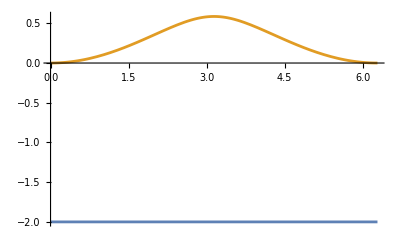

```mathematica
a00 =0.9;
Plot[{-((((md + mu)^2*(1 + Cos[x]) + 2*(md - mu)^2*Abs[Sin[x/2]]*Sin[x/2]))/(md^2 + mu^2 + 2*md*mu*Cos[x])),-Sqrt[1 -((4*mu*md)/(mu+md)^2)*Sin[x/2]^2]+1},{x,0,2*Pi}]
```

We’re very close to reproducing the axion potential, but not quite. Frustrating. It does still have the same minimum which is nice.

## Pions with axions

#### Pion mass and potential

```mathematica
Vpion = -2*a0*fπ^3 *(Mu*Cos[ϕ+θ/2]+Md*Cos[ϕ-θ/2])/.{θ->θ0+θa}
```

-2 a0 fπ^3 (Md cos((θ0+θa)/2-ϕ)+Mu cos((θ0+θa)/2+ϕ))

```mathematica
dVpiondphi = D[Vpion,ϕ]//Simplify;
phiminsols = Solve[dVpiondphi == 0, ϕ]//Simplify;
tanphimin = FullSimplify[Tan[ϕ]/.phiminsols[[1]],Assumptions->{Element[Mu|Md|θ0|θa,Reals],Mu>0,Md>0}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
tanphimin
```

(Abs[Md-Mu] sec((θ0+θa)/2) Abs[sin((θ0+θa)/2)])/(Md+Mu)

This gives the VEV of the pion. Now assume the pion oscillates about this miminum so that π  = ⟨π⟩ + π0.

```mathematica
πvev = ArcTan[tanphimin]*Sqrt[2]*fπ//Simplify;
πtot = πvev + π0;
VpionNearMin = Vpion/.{ϕ -> πtot / (Sqrt[2]*fπ)}//Simplify;
```

```mathematica
VpionNearMin
```

-2 a0 fπ^3 (Md cos(1/2 (-2 tan^-1((Abs[Md-Mu] sec((θ0+θa)/2) Abs[sin((θ0+θa)/2)])/(Md+Mu))-(√2 π0)/fπ+θ0+θa))+Mu cos(1/2 (2 tan^-1((Abs[Md-Mu] sec((θ0+θa)/2) Abs[sin((θ0+θa)/2)])/(Md+Mu))+(√2 π0)/fπ+θ0+θa)))

```mathematica
pionmassterm = Coefficient[Normal[Series[VpionNearMin,{π0,0,2}]],π0^2]//Simplify;
pionmassterm=Simplify[pionmassterm,Assumptions->{Element[Mu|Md|θ0|θa,Reals],Mu>0,Md>0,Md>Mu,θ0>0,θ0<Pi,θa>0,θa<Pi}];
pionmassterm=Simplify[TrigExpand[%],Assumptions->{Element[Mu|Md|θ0|θa,Reals],Mu>0,Md>0,Md>Mu,θ0>0,θ0<Pi,θa>0,θa<Pi}]
```

(a0 fπ sec((θ0+θa)/2) (Md^2+2 Md Mu cos(θ0+θa)+Mu^2))/(2 (Md+Mu) √(((Md-Mu)^2 tan^2((θ0+θa)/2))/(Md+Mu)^2+1))

```mathematica
FullSimplify[pionmassterm]
```

(a0 fπ sec((θ0+θa)/2) (Md^2+2 Md Mu cos(θ0+θa)+Mu^2))/(2 (Md+Mu) √(((Md-Mu)^2 tan^2((θ0+θa)/2))/(Md+Mu)^2+1))

```mathematica
pionmassterm = a0*fπ*Sqrt[Mu^2 + Md^2 + 2*Mu*Md*Cos[θ0+θa]];
```

#### axion mass and potential

```mathematica
Vaatpionmin = FullSimplify[TrigExpand[Vaatpionmin],Assumptions->{Element[Mu|Md|θ0|θa,Reals],Mu>0,Md>0,Md>Mu,θ0>0,θ0<Pi,θa>0,θa<Pi}]
```

-2 √2 a0 fπ^3 cos((θ0+θa)/2) √((Md^2+2 Md Mu cos(θ0+θa)+Mu^2)/(cos(θ0+θa)+1))

```mathematica
TrigExpand[Vaatpionmin]//Simplify
```

-2 √2 a0 fπ^3 cos((θ0+θa)/2) √((Md^2+2 Md Mu cos(θ0+θa)+Mu^2)/(cos(θ0+θa)+1))

```mathematica
dVaatpionminda =Simplify[D[Vaatpionmin,θ0],Assumptions->{Element[Mu|Md|θ0|θa,Reals],Mu>0,Md>0,Md>Mu,θ0>0,θ0<Pi,θa>0,θa<Pi}];
```

```mathematica
dVaatpionminda
```

(2 a0 fπ^3 Md Mu sin(θ0+θa) (Md cos(1/2 (θ0+θa-2 tan^-1(((Md-Mu) tan((θ0+θa)/2))/(Md+Mu))))+Mu cos(1/2 (θ0+θa+2 tan^-1(((Md-Mu) tan((θ0+θa)/2))/(Md+Mu))))))/(Md^2+2 Md Mu cos(θ0+θa)+Mu^2)

```mathematica
aminsol = Solve[dVaatpionminda==0,θa][[3]]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{θa→-2 cos^-1(cos(θ0/2))}

This shows that the axion will get a vev to cancel the theta term in the QCD Lagrangian. Now expand the axion potential around the vev to get the axion mass.

```mathematica
θavev = -θ0;
```

```mathematica
Vaatpionminnearaxionmin = Vaatpionmin/.{θa->θavev + θa}//Simplify
```

-2 a0 fπ^3 (Md cos(1/2 (θa-2 tan^-1((tan(θa/2) (Md-Mu))/(Md+Mu))))+Mu cos(θa/2+tan^-1((tan(θa/2) (Md-Mu))/(Md+Mu))))

```mathematica
Vaatpionminnearaxionmin =FullSimplify[TrigExpand[Vaatpionminnearaxionmin],Assumptions->{Element[Mu|Md|θ0|θa,Reals],Mu>0,Md>0,Md>Mu,θ0>0,θ0<Pi,θa>0,θa<Pi}]
```

-2 a0 fπ^3 √(Md^2+2 Md Mu cos(θa)+Mu^2)

```mathematica
axionmassterm = 2*Coefficient[Normal[Series[Vaatpionminnearaxionmin,{θa,0,2}]],θa^2]//Simplify
```

(2 a0 fπ^3 Md Mu)/(Md+Mu)

```mathematica
(* covariant derivative of derivative of axion field *)
covD = Derivative[1][θTp][r] + Christoffel[[mu,r,mu]]*θTp[r]

θTp[r]
```

```mathematica
But the function we're taking a derivative of is actually g^rr * θTp[r]
```

a actually But derivative function is of re taking the g^rr θTp(r) we'

```mathematica
D[-(1 - 2*M[r]/r)*θTp[r], r] + Christoffel[[mu,r,mu]]*(-(1 - 2*M[r]/r)* θTp[r])
```

```mathematica
D[-(1 - 2*M[r]/r)*θTp[r], r] + ((-4*mass[rt]*scales[[3]] - 4*Pi*rt^3*scales[[1]]^3*pressure[rt]+4*Pi*rt^3*scales[[1]]^3*density[rt]*scales[[2]]+2*rt*scales[[1]])/(rt*scales[[1]]-2*mass[rt]*scales[[3]]))*(-(1 - 2*M[r]/r)* θTp[r])
```

# Effective Axion Potential with Running Quark Masses

```mathematica
Va[θ_]:=-ϵ*mpi^2*fpi^2*(Sqrt[1 - (4*mueff*mdeff/(mueff+mdeff)^2)*Sin[θ/2]^2] - 1)
```

```mathematica
mueff = mu*(1  - (2*σN*nN/(mpi^2*fpi^2))*()
```